```mathematica
Tr = 15. (* Recombination time in Xe*)

(* For tau1 =2.2 ns, tau1 < Tr *)
I1[t_]:= (1+t/15.)^-2
```

15.

```mathematica
(* For tau2 = 27 ns, tau2 > Tr *)
I2[t_]:=Exp[-t/27.]/27.
```

```mathematica
(* We need to normalize I1 and I2*)
```

```mathematica
Integrate[I1[t],{t,0,Infinity}]
```

15.

```mathematica
NoI1[t_]:=(1/15.)*I1[t]
```

```mathematica
Integrate[NoI1[t],{t,0,Infinity}]
```

1.

```mathematica
(* I2 is already normalized *)
```

```mathematica
Integrate[I2[t],{t,0,Infinity}]
```

1.

```mathematica
(*write down the recombination intensity *)
```

```mathematica
II[t_]:=0.44*(1./15.)*I1[t]+0.56*I2[t]
```

```mathematica
Integrate[II[t],{t,0,Infinity}]
```

1.

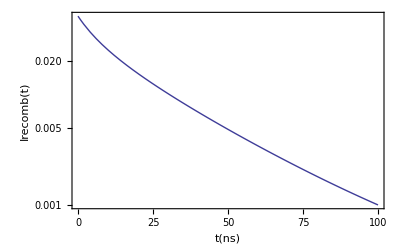

```mathematica
(* Plot the recomb intensity*)
LogPlot[II[t],{t,0.,100.},Frame->True,FrameLabel->{"t(ns)","Irecomb(t)"}]
```

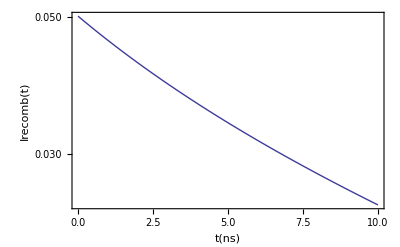

```mathematica
(* Plot the recomb intensity in the shorter range*)
LogPlot[II[t],{t,0.,10.},Frame->True,FrameLabel->{"t(ns)","Irecomb(t)"}]
```

```mathematica
(*excitation intensity *)
```

```mathematica
SI[t_]:=0.15*Exp[-t/2.2]/2.2 + 0.85 *Exp[-t/27.]/27.
```

```mathematica
(* is normalized *)
Integrate[SI[t],{t,0,Infinity}]
```

1.

```mathematica
(* Plot the scint intensity in the shorter range*)
```

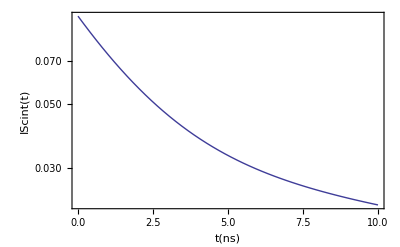

```mathematica
LogPlot[SI[t],{t,0.,10.},Frame->True,FrameLabel->{"t(ns)","IScint(t)"}]
```

```mathematica
(* total function *)
L[t_]:=0.7*II[t]+0.3*SI[t]
```

```mathematica
(* also normalized *)
```

```mathematica
Integrate[L[t],{t,0,Infinity}]
```

1.

```mathematica
(* multiply by the total number of photons*)
```

```mathematica
NG[t_]:=3 10^4*L[t]
```

```mathematica
Integrate[NG[t],{t,0,Infinity}]
```

30000.

```mathematica
(* plot in the short range)
```

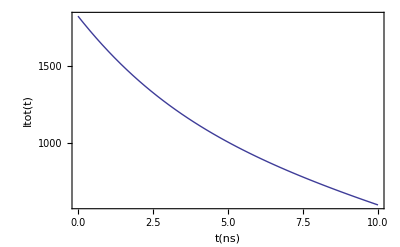

```mathematica
LogPlot[NG[t],{t,0.,10.},Frame->True,FrameLabel->{"t(ns)","Itot(t)"}]
```

```mathematica
(* plot in the long range *)
```

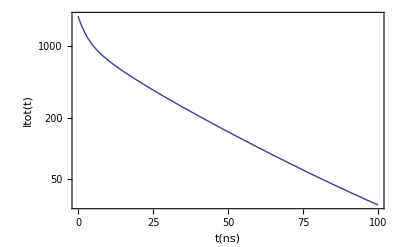

```mathematica
LogPlot[NG[t],{t,0.,100.},Frame->True,FrameLabel->{"t(ns)","Itot(t)"}]
```

```mathematica
(* plot in the medium range *)
```

```mathematica
LogPlot[NG[t],{t,0.,10.},Frame->True,FrameLabel->{"t(ns)","Itot(t)"}]
```

-Graphics-

```mathematica
(* plot in the very short range)
```

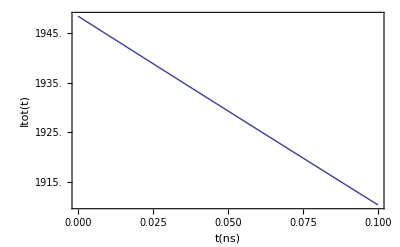

```mathematica
LogPlot[NG[t],{t,0.,0.1},Frame->True,FrameLabel->{"t(ns)","Itot(t)"}]
```

```mathematica
(* how many photons emitted in the first 100 ps?)
```

```mathematica
tb =Table[NG[t],{t,0.,0.1,0.01}]
```

{1948.53,1944.66,1940.8,1936.96,1933.13,1929.32,1925.52,1921.74,1917.97,1914.21,1910.47}

```mathematica
Total[tb]
```

21223.3

```mathematica
(* Fit to two exponentials*)
```

```mathematica
fp=Table[{t,NG[t]},{t,0.,10.,0.05}]
```

{{0.,1948.53},{0.05,1929.32},{0.1,1910.47},{0.15,1891.96},{0.2,1873.79},{0.25,1855.95},{0.3,1838.44},{0.35,1821.24},{0.4,1804.35},{0.45,1787.77},{0.5,1771.48},{0.55,1755.49},{0.6,1739.78},{0.65,1724.35},{0.7,1709.19},{0.75,1694.3},{0.8,1679.67},{0.85,1665.29},{0.9,1651.17},{0.95,1637.29},{1.,1623.65},{1.05,1610.25},{1.1,1597.08},{1.15,1584.13},{1.2,1571.41},{1.25,1558.9},{1.3,1546.6},{1.35,1534.51},{1.4,1522.63},{1.45,1510.94},{1.5,1499.44},{1.55,1488.14},{1.6,1477.03},{1.65,1466.09},{1.7,1455.34},{1.75,1444.76},{1.8,1434.35},{1.85,1424.12},{1.9,1414.04},{1.95,1404.13},{2.,1394.38},{2.05,1384.78},{2.1,1375.33},{2.15,1366.03},{2.2,1356.88},{2.25,1347.87},{2.3,1338.99},{2.35,1330.26},{2.4,1321.66},{2.45,1313.19},{2.5,1304.85},{2.55,1296.64},{2.6,1288.55},{2.65,1280.58},{2.7,1272.73},{2.75,1265.},{2.8,1257.38},{2.85,1249.87},{2.9,1242.47},{2.95,1235.18},{3.,1227.99},{3.05,1220.91},{3.1,1213.93},{3.15,1207.04},{3.2,1200.26},{3.25,1193.57},{3.3,1186.97},{3.35,1180.46},{3.4,1174.05},{3.45,1167.72},{3.5,1161.48},{3.55,1155.32},{3.6,1149.24},{3.65,1143.25},{3.7,1137.34},{3.75,1131.5},{3.8,1125.74},{3.85,1120.06},{3.9,1114.45},{3.95,1108.91},{4.,1103.44},{4.05,1098.04},{4.1,1092.71},{4.15,1087.45},{4.2,1082.25},{4.25,1077.12},{4.3,1072.05},{4.35,1067.04},{4.4,1062.1},{4.45,1057.21},{4.5,1052.38},{4.55,1047.61},{4.6,1042.89},{4.65,1038.23},{4.7,1033.63},{4.75,1029.08},{4.8,1024.58},{4.85,1020.13},{4.9,1015.73},{4.95,1011.38},{5.,1007.08},{5.05,1002.83},{5.1,998.627},{5.15,994.468},{5.2,990.354},{5.25,986.285},{5.3,982.259},{5.35,978.275},{5.4,974.334},{5.45,970.434},{5.5,966.575},{5.55,962.755},{5.6,958.974},{5.65,955.232},{5.7,951.528},{5.75,947.86},{5.8,944.229},{5.85,940.634},{5.9,937.074},{5.95,933.549},{6.,930.057},{6.05,926.599},{6.1,923.174},{6.15,919.781},{6.2,916.42},{6.25,913.09},{6.3,909.79},{6.35,906.521},{6.4,903.281},{6.45,900.071},{6.5,896.889},{6.55,893.735},{6.6,890.609},{6.65,887.511},{6.7,884.439},{6.75,881.393},{6.8,878.374},{6.85,875.38},{6.9,872.411},{6.95,869.467},{7.,866.547},{7.05,863.651},{7.1,860.779},{7.15,857.929},{7.2,855.103},{7.25,852.299},{7.3,849.517},{7.35,846.757},{7.4,844.019},{7.45,841.301},{7.5,838.605},{7.55,835.929},{7.6,833.272},{7.65,830.636},{7.7,828.02},{7.75,825.422},{7.8,822.844},{7.85,820.284},{7.9,817.743},{7.95,815.219},{8.,812.714},{8.05,810.226},{8.1,807.756},{8.15,805.303},{8.2,802.866},{8.25,800.446},{8.3,798.043},{8.35,795.656},{8.4,793.284},{8.45,790.929},{8.5,788.589},{8.55,786.264},{8.6,783.954},{8.65,781.659},{8.7,779.379},{8.75,777.113},{8.8,774.861},{8.85,772.624},{8.9,770.4},{8.95,768.19},{9.,765.994},{9.05,763.811},{9.1,761.641},{9.15,759.484},{9.2,757.34},{9.25,755.208},{9.3,753.089},{9.35,750.983},{9.4,748.888},{9.45,746.806},{9.5,744.735},{9.55,742.676},{9.6,740.629},{9.65,738.593},{9.7,736.569},{9.75,734.555},{9.8,732.553},{9.85,730.562},{9.9,728.581},{9.95,726.611},{10.,724.651}}

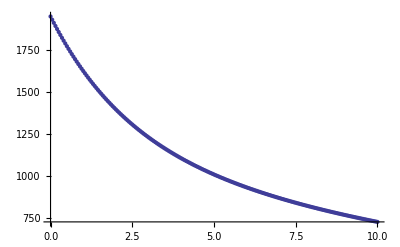

```mathematica
gp=ListPlot[fp]
```

```mathematica
model2 =a*Exp[-t/2.2]+b*Exp[-t/27.]
```

a ⅇ^(-0.454545 t)+b ⅇ^(-0.037037 t)

```mathematica
fit2 = FindFit[fp,model2,{a,b},t]
```

{a→911.082,b→1084.64}

```mathematica
modelf2=Function[{t},Evaluate[model2/.fit2]]
```

Function[{t},911.082 ⅇ^(-0.454545 t)+1084.64 ⅇ^(-0.037037 t)]

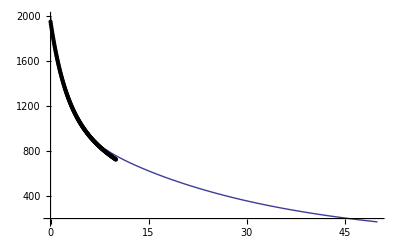

```mathematica
Plot[modelf2[t],{t,0,50},Epilog->Map[Point,fp]]
```

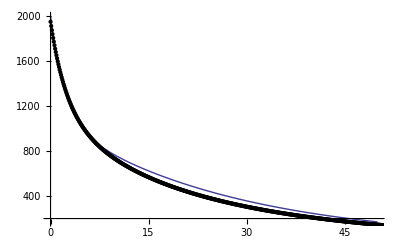

```mathematica
Plot[modelf2[t],{t,0,50},Epilog->Map[Point,fp2]]
```

```mathematica
P1 = LogPlot[NG[t],{t,0.,100.},Frame->True,FrameLabel->{"t(ns)","Itot(t)"}]
```

-Graphics-

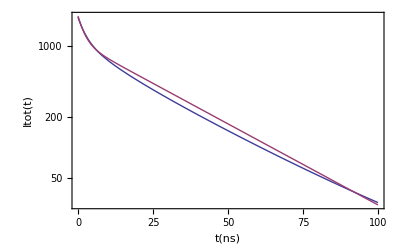

```mathematica
P2 = LogPlot[{NG[t],modelf2[t]},{t,0.,100.},Frame->True,FrameLabel->{"t(ns)","Itot(t)"}]
```

```mathematica
(* how good is the fit at short times? *)
tb =Table[modelf2[t],{t,0.,0.1,0.01}]
```

{1995.73,1991.19,1986.68,1982.18,1977.71,1973.25,1968.81,1964.39,1959.98,1955.6,1951.23}

```mathematica
Total[tb]
```

21706.7

```mathematica
(* and in total *)
tb =Table[modelf2[t],{t,0.,100.,1.}]
```

{1995.73,1623.5,1374.27,1203.57,1083.18,995.155,928.098,874.756,830.511,792.419,758.595,727.832,699.349,672.64,647.369,623.315,600.324,578.288,557.13,536.789,517.218,498.379,480.237,462.762,445.927,429.708,414.081,399.023,384.513,370.531,357.058,344.076,331.565,319.509,307.892,296.697,285.909,275.514,265.496,255.843,246.54,237.576,228.938,220.614,212.593,204.863,197.414,190.236,183.319,176.654,170.231,164.041,158.077,152.329,146.791,141.453,136.31,131.354,126.578,121.976,117.541,113.267,109.149,105.18,101.356,97.6706,94.1193,90.6972,87.3995,84.2217,81.1594,78.2085,75.3648,72.6246,69.984,67.4394,64.9874,62.6244,60.3475,58.1532,56.0388,54.0013,52.0378,50.1457,48.3225,46.5655,44.8724,43.2408,41.6686,40.1536,38.6936,37.2867,35.931,34.6246,33.3656,32.1525,30.9834,29.8569,28.7713,27.7252,26.7171}

```mathematica
Total[tb]
```

31617.3

```mathematica
model4 =a*Exp[-t/2.2]+b*Exp[-t/25.]
```

a ⅇ^(-0.454545 t)+b ⅇ^(-0.04 t)

```mathematica
fit3 = FindFit[fp,model4,{a,b},t]
```

{a→880.581,b→1107.75}

```mathematica
modelf3=Function[{t},Evaluate[model4/.fit3]]
```

Function[{t},880.581 ⅇ^(-0.454545 t)+1107.75 ⅇ^(-0.04 t)]

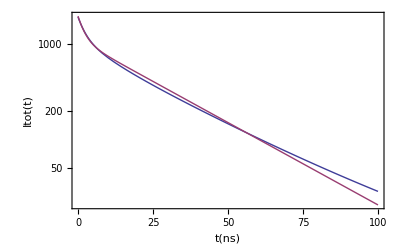

```mathematica
LogPlot[{NG[t],modelf3[t]},{t,0.,100.},Frame->True,FrameLabel->{"t(ns)","Itot(t)"}]
```